```mathematica
(*Homework 30*)
F[x_]:= (x^2)^2
F'[x]
```

4 x^3

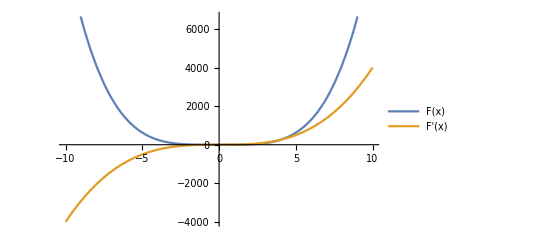

```mathematica
Plot[{F[x],F'[x]},{x,-10,10},PlotLegends->"Expressions"]
```

```mathematica
(*Homework 31*)
f[x_]:=(-7/4)+(1/4)*(49-8*(x^2-(5*x)-40))^(1/2)
f1[x_]:=(-7/4)-(1/4)*(49-8*(x^2-(5*x)-40))^(1/2)
g[x_]:=1+(-1/2)(4-4*(-1)(3*x^2+4*x-28))^(1/2)
g1[x_]:=1-(-1/2)(4-4*(-1)(3*x^2+4*x-28))^(1/2)
```

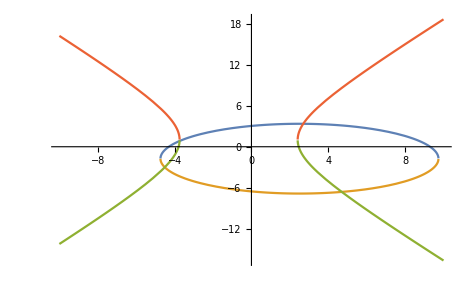

```mathematica
Plot[{f[x],f1[x],g[x],g1[x]},{x,-10,10}]
```

```mathematica
f[x_,y_]:=x^2+2y^2-5x+7y-40==0
```

```mathematica
g[x_,y_]:=3x^2-y^2+4x+2y-28==0

(*Graphical Solutions; coordinates left most to right most*)
(*Using Get Coordinates*)
(*(-4.5546,-2.90581),(-3.78574,0.901333),(2.69967,3.53835),(4.67725,-6.55108)*)
```

```mathematica
(*Solutions using solve*)
```

```mathematica
Solve[{f[x,y],g[x,y]},{x,y}]
```

```mathematica
Solve[{f[x],g[x]},{x,y}]
```

Solve::naqs: -7/4+1/4 √(49-8 (-40+Times[«2»]+Power[«2»]))&&1-1/2 √(4+4 (-28+Times[«2»]+Times[«2»])) is not a quantified system of equations and inequalities.

Solve[{-7/4+1/4 √(49-8 (-40-5 x+x^2)),1-1/2 √(4+4 (-28+4 x+3 x^2))},{x,y}]

```mathematica
Solve[{f1[x],g1[x]},{x,y}]
```

Solve::naqs: -7/4-1/4 √(49-8 (-40+Times[«2»]+Power[«2»]))&&1+1/2 √(4+4 (-28+Times[«2»]+Times[«2»])) is not a quantified system of equations and inequalities.

Solve[{-7/4-1/4 √(49-8 (-40-5 x+x^2)),1+1/2 √(4+4 (-28+4 x+3 x^2))},{x,y}]

```mathematica
Solve[{f[x,y],g[x,y]},{x,y}]
```

{{x→-3/14-1/14 √(1/3 (3115+(4339238 2^(2/3))/(12754379543+2541 ⅈ √113480785095)^(1/3)+(2 (12754379543+2541 ⅈ √113480785095))^(1/3)))-1/2 √(890/21-(4339238 2^(2/3))/(147 (12754379543+2541 ⅈ √113480785095)^(1/3))-1/147 (2 (12754379543+2541 ⅈ √113480785095))^(1/3)-4598/(49 √(1/3 (3115+(4339238 2^(2/3))/(12754379543+2541 ⅈ √113480785095)^(1/3)+(2 (12754379543+2541 ⅈ √113480785095))^(1/3))))),y→1/11 (-209/14+2299/(14 √(1/3 (3115+(4339238 2^(2/3))/(12754379543+2541 ⅈ √113480785095)^(1/3)+(2 (12754379543+2541 ⅈ √113480785095))^(1/3))))-1/2 √(1/3 (3115+(4339238 2^(2/3))/(12754379543+2541 ⅈ √113480785095)^(1/3)+(2 (12754379543+2541 ⅈ √113480785095))^(1/3))) √(890/21-(4339238 2^(2/3))/(147 (12754379543+2541 ⅈ √113480785095)^(1/3))-1/147 (2 (12754379543+2541 ⅈ √113480785095))^(1/3)-4598/(49 √(1/3 (3115+(4339238 2^(2/3))/(12754379543+2541 ⅈ √113480785095)^(1/3)+(2 (12754379543+2541 ⅈ √113480785095))^(1/3))))))},{x→-3/14-1/14 √(1/3 (3115+(4339238 2^(2/3))/(12754379543+2541 ⅈ √113480785095)^(1/3)+(2 (12754379543+2541 ⅈ √113480785095))^(1/3)))+1/2 √(890/21-(4339238 2^(2/3))/(147 (12754379543+2541 ⅈ √113480785095)^(1/3))-1/147 (2 (12754379543+2541 ⅈ √113480785095))^(1/3)-4598/(49 √(1/3 (3115+(4339238 2^(2/3))/(12754379543+2541 ⅈ √113480785095)^(1/3)+(2 (12754379543+2541 ⅈ √113480785095))^(1/3))))),y→1/11 (-209/14+2299/(14 √(1/3 (3115+(4339238 2^(2/3))/(12754379543+2541 ⅈ √113480785095)^(1/3)+(2 (12754379543+2541 ⅈ √113480785095))^(1/3))))+1/2 √(1/3 (3115+(4339238 2^(2/3))/(12754379543+2541 ⅈ √113480785095)^(1/3)+(2 (12754379543+2541 ⅈ √113480785095))^(1/3))) √(890/21-(4339238 2^(2/3))/(147 (12754379543+2541 ⅈ √113480785095)^(1/3))-1/147 (2 (12754379543+2541 ⅈ √113480785095))^(1/3)-4598/(49 √(1/3 (3115+(4339238 2^(2/3))/(12754379543+2541 ⅈ √113480785095)^(1/3)+(2 (12754379543+2541 ⅈ √113480785095))^(1/3))))))},{x→-3/14+1/14 √(1/3 (3115+(4339238 2^(2/3))/(12754379543+2541 ⅈ √113480785095)^(1/3)+(2 (12754379543+2541 ⅈ √113480785095))^(1/3)))-1/2 √(890/21-(4339238 2^(2/3))/(147 (12754379543+2541 ⅈ √113480785095)^(1/3))-1/147 (2 (12754379543+2541 ⅈ √113480785095))^(1/3)+4598/(49 √(1/3 (3115+(4339238 2^(2/3))/(12754379543+2541 ⅈ √113480785095)^(1/3)+(2 (12754379543+2541 ⅈ √113480785095))^(1/3))))),y→1/11 (-209/14-2299/(14 √(1/3 (3115+(4339238 2^(2/3))/(12754379543+2541 ⅈ √113480785095)^(1/3)+(2 (12754379543+2541 ⅈ √113480785095))^(1/3))))+1/2 √(1/3 (3115+(4339238 2^(2/3))/(12754379543+2541 ⅈ √113480785095)^(1/3)+(2 (12754379543+2541 ⅈ √113480785095))^(1/3))) √(890/21-(4339238 2^(2/3))/(147 (12754379543+2541 ⅈ √113480785095)^(1/3))-1/147 (2 (12754379543+2541 ⅈ √113480785095))^(1/3)+4598/(49 √(1/3 (3115+(4339238 2^(2/3))/(12754379543+2541 ⅈ √113480785095)^(1/3)+(2 (12754379543+2541 ⅈ √113480785095))^(1/3))))))},{x→-3/14+1/14 √(1/3 (3115+(4339238 2^(2/3))/(12754379543+2541 ⅈ √113480785095)^(1/3)+(2 (12754379543+2541 ⅈ √113480785095))^(1/3)))+1/2 √(890/21-(4339238 2^(2/3))/(147 (12754379543+2541 ⅈ √113480785095)^(1/3))-1/147 (2 (12754379543+2541 ⅈ √113480785095))^(1/3)+4598/(49 √(1/3 (3115+(4339238 2^(2/3))/(12754379543+2541 ⅈ √113480785095)^(1/3)+(2 (12754379543+2541 ⅈ √113480785095))^(1/3))))),y→1/11 (-209/14-2299/(14 √(1/3 (3115+(4339238 2^(2/3))/(12754379543+2541 ⅈ √113480785095)^(1/3)+(2 (12754379543+2541 ⅈ √113480785095))^(1/3))))-1/2 √(1/3 (3115+(4339238 2^(2/3))/(12754379543+2541 ⅈ √113480785095)^(1/3)+(2 (12754379543+2541 ⅈ √113480785095))^(1/3))) √(890/21-(4339238 2^(2/3))/(147 (12754379543+2541 ⅈ √113480785095)^(1/3))-1/147 (2 (12754379543+2541 ⅈ √113480785095))^(1/3)+4598/(49 √(1/3 (3115+(4339238 2^(2/3))/(12754379543+2541 ⅈ √113480785095)^(1/3)+(2 (12754379543+2541 ⅈ √113480785095))^(1/3))))))}}